### H[] is the core matrix for hamiltonian in k-space, there are 3 different sites.

```mathematica
H[kx_,ky_]:=-2({{0, Cos[-kx/2-Sqrt[3]ky/2], Cos[-kx/2+Sqrt[3]ky/2]}, {Cos[-kx/2-Sqrt[3]ky/2], 0, Cos[kx]}, {Cos[-kx/2+Sqrt[3]ky/2], Cos[kx], 0}});
```

### Dispersion relation E[kx,ky]

```mathematica
Eigensystem[H[kx,ky]]
```

{{2,-1-√(3+2 Cos[2 kx]+2 Cos[kx-√3 ky]+2 Cos[kx+√3 ky]),-1+√(3+2 Cos[2 kx]+2 Cos[kx-√3 ky]+2 Cos[kx+√3 ky])},{{-(-Cos[kx/2-(√3 ky)/2]+Cos[kx] Cos[kx/2+(√3 ky)/2])/(-1+Cos[kx/2+(√3 ky)/2]^2),-(-Cos[kx]+Cos[kx/2-(√3 ky)/2] Cos[kx/2+(√3 ky)/2])/(-1+Cos[kx/2+(√3 ky)/2]^2),1},{((2-2 Cos[kx]^2+Cos[2 kx]+Cos[kx-√3 ky]+Cos[kx+√3 ky]+√(3+2 Cos[2 kx]+2 Cos[kx-√3 ky]+2 Cos[kx+√3 ky])) Sec[kx/2-(√3 ky)/2])/(1+√(3+2 Cos[2 kx]+2 Cos[kx-√3 ky]+2 Cos[kx+√3 ky])+2 Cos[kx] Cos[kx/2+(√3 ky)/2] Sec[kx/2-(√3 ky)/2]),-(4 Cos[kx] Cos[kx/2-(√3 ky)/2]+2 Cos[kx/2+(√3 ky)/2] (1+√(3+2 Cos[2 kx]+2 Cos[kx-√3 ky]+2 Cos[kx+√3 ky])))/(-4 Cos[kx] Cos[kx/2+(√3 ky)/2]-2 Cos[kx/2-(√3 ky)/2] (1+√(3+2 Cos[2 kx]+2 Cos[kx-√3 ky]+2 Cos[kx+√3 ky]))),1},{((-2+2 Cos[kx]^2-Cos[2 kx]-Cos[kx-√3 ky]-Cos[kx+√3 ky]+√(3+2 Cos[2 kx]+2 Cos[kx-√3 ky]+2 Cos[kx+√3 ky])) Sec[kx/2-(√3 ky)/2])/(-1+√(3+2 Cos[2 kx]+2 Cos[kx-√3 ky]+2 Cos[kx+√3 ky])-2 Cos[kx] Cos[kx/2+(√3 ky)/2] Sec[kx/2-(√3 ky)/2]),-(4 Cos[kx] Cos[kx/2-(√3 ky)/2]+2 Cos[kx/2+(√3 ky)/2] (1-√(3+2 Cos[2 kx]+2 Cos[kx-√3 ky]+2 Cos[kx+√3 ky])))/(-4 Cos[kx] Cos[kx/2+(√3 ky)/2]-2 Cos[kx/2-(√3 ky)/2] (1-√(3+2 Cos[2 kx]+2 Cos[kx-√3 ky]+2 Cos[kx+√3 ky]))),1}}}

```mathematica
EE[kx_,ky_]:=Sort[Eigenvalues[H[kx,ky]]];
```

### 3D Plot

```mathematica
Plot3D[EE[x,y],{x,-2Pi/3,2Pi/3},{y,-Pi/Sqrt[3],Pi/Sqrt[3]},RegionFunction->Function[{x,y,z},Abs[x+y/Sqrt[3]]≤2Pi/3&&Abs[x-y/Sqrt[3]]≤2Pi/3],AxesLabel->{kx,ky,Energy}]
```

-Graphics3D-

### 1D High symmetry Brillouin zone point loop plot

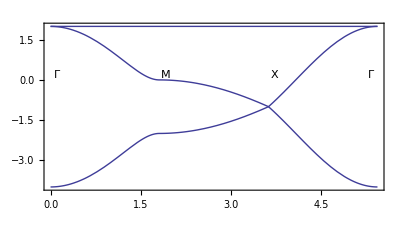

```mathematica
Plot[Piecewise[{{EE[t Sqrt[3]/2,t/2],t≥0&&t<Pi/Sqrt[3]},{EE[Sqrt[3]((t-Pi/Sqrt[3])/3+Pi/Sqrt[3])/2,(2Pi/3-t/Sqrt[3])Sqrt[3]/2],t≥Pi/Sqrt[3]&&t<2Pi/Sqrt[3]},{EE[2(Pi/Sqrt[3]-(t-2Pi/Sqrt[3]))/Sqrt[3],0],t≥2Pi/Sqrt[3]&&t<3Pi/Sqrt[3]}}],{t,0,Sqrt[3]Pi},GridLines->{{{Pi/Sqrt[3],Dashed},{2Pi/Sqrt[3],Dashed},{0,Dashed},{3Pi/Sqrt[3],Dashed}},{}},Epilog->{Inset["Γ",{0.1,0.2}],Inset["M",{Pi/Sqrt[3]+0.1,0.2}],Inset["X",{2Pi/Sqrt[3]+0.1,0.2}],Inset["Γ",{3Pi/Sqrt[3]-0.1,0.2}],Inset[Style["k",16],{5,-5.5}],Inset[Style["Energy",16],{0.4,2.5}]},Frame->True]
```

```mathematica
EEE[x_,y_]:={-1-√(3+2 Cos[x Sqrt[3]]+2 Cos[√3 x/2- 3y/2]+2 Cos[Sqrt[3]x/2+3 y/2]),-1+√(3+2 Cos[Sqrt[3]x]+2 Cos[Sqrt[3]x/2-3 y/2]+2 Cos[Sqrt[3]x/2+3 y/2])}
```

```mathematica
Array[EN,400];
```

```mathematica
nn=1;While[nn<401,EN[nn]=0;nn++];
```

```mathematica
For[i=0,i≤200,i++,
For[j=0,j≤200,j++,
{
energy=EEE[i Pi/Sqrt[3]/100-Pi/Sqrt[3],2j Pi/3/100-2Pi/3]//N;    (* make sure energy is represented in the form 1.234 and not Cos[...] *)
n=Rescale[energy[[1]],{-4.5,2.2},{1,400}]//Round;    (* find appropriate bin for band 1*)
EN[n]++;
n=Rescale[energy[[2]],{-4.5,2.2},{1,400}]//Round;    (* find appropriate bin for band 2*)
EN[n]++
}
]
]
```

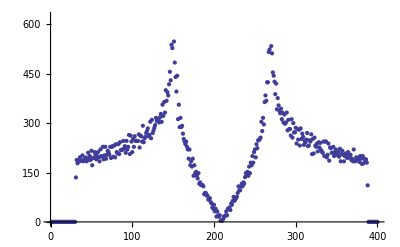

```mathematica
ListPlot[Table[{i,EN[i]},{i,1,400}]]
```

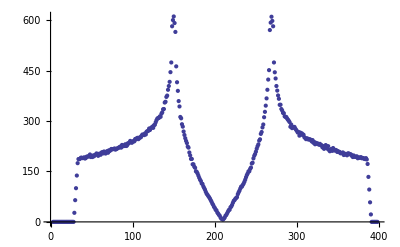

```mathematica
ListPlot[Table[{i,(EN[i-1]+EN[i-2]+EN[i]+EN[i+1]+EN[i+2])/5},{i,3,398}]]
```